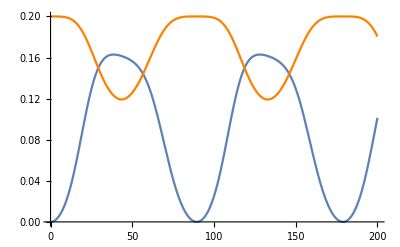

```mathematica
ClearAll["Global`*"];
subtractAngles[a1_,a2_]:=(
d=RealAbs[a1-a2];
Return[Min[d,2*Pi-d]];
);
angularError[vec_,vecError_,rx_,ry_,rz_,t_,i_]:=(
sphericalVec=ToSphericalCoordinates[vec.MatrixPower[N[EulerMatrix[{rx,ry,rz}]],t]];
sphericalVecError=ToSphericalCoordinates[vecError.MatrixPower[N[EulerMatrix[{rx,ry,rz}]],t]];
Return[subtractAngles[sphericalVec[[i]],sphericalVecError[[i]]]];
);
elevationErrorPlot=Plot[angularError[{1,0,0},N[{1,0,0}.EulerMatrix[{0,0.2,0}]],Pi/100,Pi/100,Pi/100,t,2],{t,0,200},PlotStyle->Orange];
azimuthalErrorPlot=Plot[angularError[{1,0,0},N[{1,0,0}.EulerMatrix[{0,0.2,0}]],Pi/100,Pi/100,Pi/100,t,3],{t,0,200}];
Show[azimuthalErrorPlot,elevationErrorPlot,PlotRange->All]
```

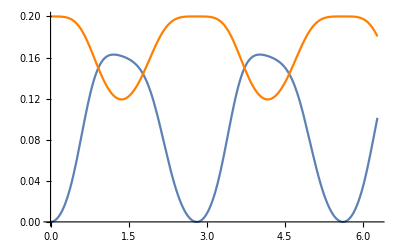

```mathematica
SP[t_]:={{Cos[√5 t],-((2 Sin[√5 t])/(√5)),Sin[√5 t]/(√5)},{(2 Sin[√5 t])/(√5),(1/5) (1+4 Cos[√5 t]),-(2/5) (-1+Cos[√5 t])},{-(Sin[√5 t]/(√5)),-(2/5) (-1+Cos[√5 t]),(1/5) (4+Cos[√5 t])}};
angularErrorSimplified[vec_,vecError_,t_,i_]:=(
sphericalVec=ToSphericalCoordinates[vec.SP[t]];
sphericalVecError=ToSphericalCoordinates[vecError.SP[t]];
Return[subtractAngles[sphericalVec[[i]],sphericalVecError[[i]]]];
);
elevationErrorPlotSimplified=Plot[angularErrorSimplified[{1,0,0},N[{1,0,0}.EulerMatrix[{0,0.2,0}]],t,2],{t,0,2Pi},PlotStyle->Orange];
azimuthalErrorPlotSimplified=Plot[angularErrorSimplified[{1,0,0},N[{1,0,0}.EulerMatrix[{0,0.2,0}]],t,3],{t,0,2Pi}];
Show[azimuthalErrorPlotSimplified,elevationErrorPlotSimplified,PlotRange->All]
```

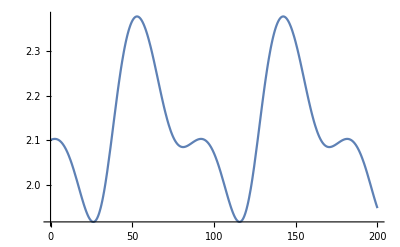

```mathematica
azimuthalError[errx_,erry_,errz_,s_,t_]:=(mp=MatrixPower[N[EulerMatrix[{2 Pi/s,2 Pi/s,2 Pi/s}]],t];
sphericalVec=ToSphericalCoordinates[{1,0,0}.mp];
sphericalVecError=ToSphericalCoordinates[{1,0,0}.EulerMatrix[{errx,erry,errz}].mp];
Return[subtractAngles[sphericalVec[[3]],sphericalVecError[[3]]]];);
Plot[azimuthalError[1.5,2,0.5,200,t],{t,0,200},PlotRange->All]
```

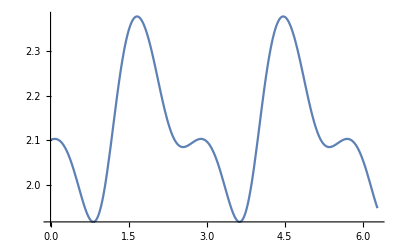

```mathematica
ClearAll["Global`*"];
subtractAngles[a1_,a2_]:=(
d=RealAbs[a1-a2];
Return[Min[d,2*Pi-d]];
);
SP[t_]:={{Cos[√5 t],-(2 Sin[√5 t])/(√5),Sin[√5 t]/(√5)},{(2 Sin[√5 t])/(√5),1/5 (1+4 Cos[√5 t]),-2/5 (-1+Cos[√5 t])},{-Sin[√5 t]/(√5),-2/5 (-1+Cos[√5 t]),1/5 (4+Cos[√5 t])}};
azimuthalErrorSimplified[errx_,erry_,errz_,t_]:=(
sphericalVec=ToSphericalCoordinates[{1,0,0}.SP[t]];
sphericalVecError=ToSphericalCoordinates[{1,0,0}.EulerMatrix[{errx,erry,errz}].SP[t]];
Return[subtractAngles[sphericalVec[[3]],sphericalVecError[[3]]]];);
Plot[azimuthalErrorSimplified[1.5,2,0.5,t],{t,0,2Pi},PlotRange->All]
```

{2.03444,{x→5.77303,y→4.30282,z→4.60239,t→3.51131}}

{3.14159,{x→1.69743,y→6.20251,z→1.45635,t→3.9524}}

{9.29501×10^-12,{x→1.6953,y→1.54656,z→4.60818,t→4.06181}}

{1.66212×10^-11,{x→5.01716,y→3.95797,z→1.78529,t→2.91116}}

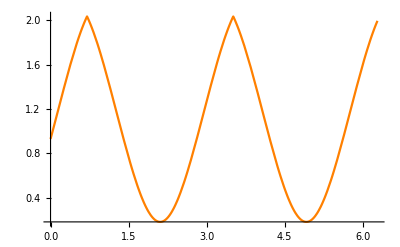

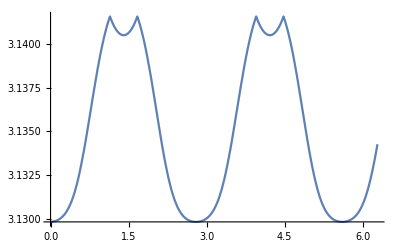

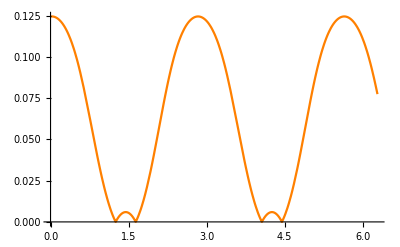

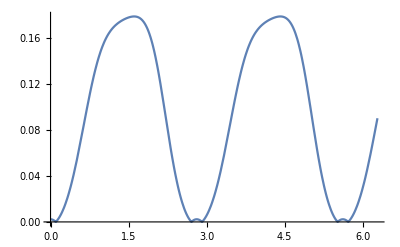

{3.14159,{x→3.37396,y→3.14159,z→2.848,t→2.80993}}

{3.14159,{x→3.11735,y→3.14159,z→4.29209,t→4.5552}}

{1.46549×10^-13,{x→5.65117,y→6.2831,z→0.890261,t→6.27776}}

{0.,{x→1.62652,y→6.28319,z→0.183988,t→6.2522}}

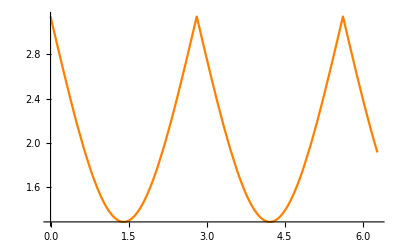

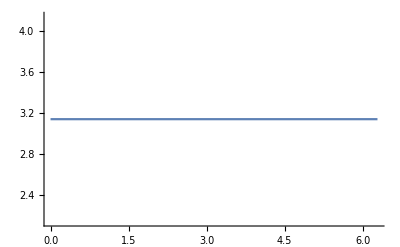

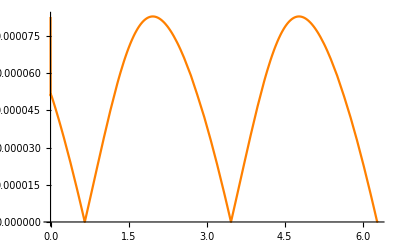

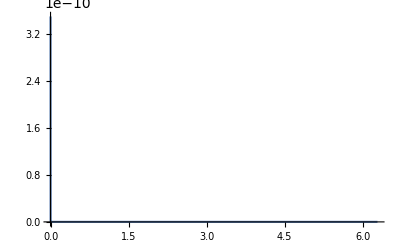

(2 π)/(√5)

(2 π)/(√5)

Piecewise[{{-(2 (-1+Cos[√5 t]) Cos[√5 t])/(5 (4/25 (-1+Cos[√5 t])^2+1/5 Sin[√5 t]^2))-(2 Sin[√5 t]^2)/(5 (4/25 (-1+Cos[√5 t])^2+1/5 Sin[√5 t]^2))-((-Cos[√5 t] Cos[y]+√5 Cos[z] Sin[√5 t] Sin[y]+2 Cos[√5 t] Sin[y] Sin[z]) (2/5 (-1+Cos[√5 t]) Cos[y]-(2 Cos[z] Sin[√5 t] Sin[y])/(√5)-1/5 (1+4 Cos[√5 t]) Sin[y] Sin[z]))/((-2/5 (-1+Cos[√5 t]) Cos[y]+(2 Cos[z] Sin[√5 t] Sin[y])/(√5)+1/5 (1+4 Cos[√5 t]) Sin[y] Sin[z])^2+(-(Cos[y] Sin[√5 t])/(√5)-Cos[√5 t] Cos[z] Sin[y]+(2 Sin[√5 t] Sin[y] Sin[z])/(√5))^2)-(((2 Cos[y] Sin[√5 t])/(√5)+2 Cos[√5 t] Cos[z] Sin[y]-(4 Sin[√5 t] Sin[y] Sin[z])/(√5)) (-(Cos[y] Sin[√5 t])/(√5)-Cos[√5 t] Cos[z] Sin[y]+(2 Sin[√5 t] Sin[y] Sin[z])/(√5)))/((-2/5 (-1+Cos[√5 t]) Cos[y]+(2 Cos[z] Sin[√5 t] Sin[y])/(√5)+1/5 (1+4 Cos[√5 t]) Sin[y] Sin[z])^2+(-(Cos[y] Sin[√5 t])/(√5)-Cos[√5 t] Cos[z] Sin[y]+(2 Sin[√5 t] Sin[y] Sin[z])/(√5))^2), 0≤ArcTan[-Sin[√5 t]/(√5),-2/5 (-1+Cos[√5 t])]-ArcTan[-(Cos[y] Sin[√5 t])/(√5)-Cos[√5 t] Cos[z] Sin[y]+(2 Sin[√5 t] Sin[y] Sin[z])/(√5),-2/5 (-1+Cos[√5 t]) Cos[y]+(2 Cos[z] Sin[√5 t] Sin[y])/(√5)+1/5 (1+4 Cos[√5 t]) Sin[y] Sin[z]]<π||ArcTan[-Sin[√5 t]/(√5),-2/5 (-1+Cos[√5 t])]-ArcTan[-(Cos[y] Sin[√5 t])/(√5)-Cos[√5 t] Cos[z] Sin[y]+(2 Sin[√5 t] Sin[y] Sin[z])/(√5),-2/5 (-1+Cos[√5 t]) Cos[y]+(2 Cos[z] Sin[√5 t] Sin[y])/(√5)+1/5 (1+4 Cos[√5 t]) Sin[y] Sin[z]]≤-π}, {(2 (-1+Cos[√5 t]) Cos[√5 t])/(5 (4/25 (-1+Cos[√5 t])^2+1/5 Sin[√5 t]^2))+(2 Sin[√5 t]^2)/(5 (4/25 (-1+Cos[√5 t])^2+1/5 Sin[√5 t]^2))+((-Cos[√5 t] Cos[y]+√5 Cos[z] Sin[√5 t] Sin[y]+2 Cos[√5 t] Sin[y] Sin[z]) (2/5 (-1+Cos[√5 t]) Cos[y]-(2 Cos[z] Sin[√5 t] Sin[y])/(√5)-1/5 (1+4 Cos[√5 t]) Sin[y] Sin[z]))/((-2/5 (-1+Cos[√5 t]) Cos[y]+(2 Cos[z] Sin[√5 t] Sin[y])/(√5)+1/5 (1+4 Cos[√5 t]) Sin[y] Sin[z])^2+(-(Cos[y] Sin[√5 t])/(√5)-Cos[√5 t] Cos[z] Sin[y]+(2 Sin[√5 t] Sin[y] Sin[z])/(√5))^2)+(((2 Cos[y] Sin[√5 t])/(√5)+2 Cos[√5 t] Cos[z] Sin[y]-(4 Sin[√5 t] Sin[y] Sin[z])/(√5)) (-(Cos[y] Sin[√5 t])/(√5)-Cos[√5 t] Cos[z] Sin[y]+(2 Sin[√5 t] Sin[y] Sin[z])/(√5)))/((-2/5 (-1+Cos[√5 t]) Cos[y]+(2 Cos[z] Sin[√5 t] Sin[y])/(√5)+1/5 (1+4 Cos[√5 t]) Sin[y] Sin[z])^2+(-(Cos[y] Sin[√5 t])/(√5)-Cos[√5 t] Cos[z] Sin[y]+(2 Sin[√5 t] Sin[y] Sin[z])/(√5))^2), True}}]

```mathematica
ClearAll["Global`*"];
subtractAngles[a1_,a2_]:=(
d=RealAbs[a1-a2];
Return[Min[d,2*Pi-d]];
);
SP[t_]:={{Cos[√5 t],-((2 Sin[√5 t])/(√5)),Sin[√5 t]/(√5)},{(2 Sin[√5 t])/(√5),(1/5) (1+4 Cos[√5 t]),-(2/5) (-1+Cos[√5 t])},{-(Sin[√5 t]/(√5)),-(2/5) (-1+Cos[√5 t]),(1/5) (4+Cos[√5 t])}};
angularErrorSimplified[vec_,vecError_,t_,i_]:=(
sphericalVec=ToSphericalCoordinates[vec.SP[t]];
sphericalVecError=ToSphericalCoordinates[vecError.SP[t]];
Return[subtractAngles[sphericalVec[[i]],sphericalVecError[[i]]]];
);
elevationErrorSimplified[errx_,erry_,errz_,t_]:=angularErrorSimplified[{1,0,0},{1,0,0}.EulerMatrix[{errx,erry,errz}],t,2];
azimuthalErrorSimplified[errx_,erry_,errz_,t_]:=angularErrorSimplified[{1,0,0},{1,0,0}.EulerMatrix[{errx,erry,errz}],t,3];
(*FindMaximum[elevationErrorSimplified[x,y,z,t]&&0<x<2Pi&&0<y<2Pi&&0<z<2Pi&&0<t<2Pi,{x,y,z,t}]
FindMaximum[azimuthalErrorSimplified[x,y,z,t]&&0<x<2Pi&&0<y<2Pi&&0<z<2Pi&&0<t<2Pi,{x,y,z,t}]
FindMinimum[elevationErrorSimplified[x,y,z,t]&&0<x<2Pi&&0<y<2Pi&&0<z<2Pi&&0<t<2Pi,{x,y,z,t}]
FindMinimum[azimuthalErrorSimplified[x,y,z,t]&&0<x<2Pi&&0<y<2Pi&&0<z<2Pi&&0<t<2Pi,{x,y,z,t}]*)
NMaximize[{elevationErrorSimplified[x,y,z,t],0<x<2Pi&&0<y<2Pi&&0<z<2Pi&&0<t<2Pi},{x,y,z,t}]
NMaximize[{azimuthalErrorSimplified[x,y,z,t],0<x<2Pi&&0<y<2Pi&&0<z<2Pi&&0<t<2Pi},{x,y,z,t}]
NMinimize[{elevationErrorSimplified[x,y,z,t],0<x<2Pi&&0<y<2Pi&&0<z<2Pi&&0<t<2Pi},{x,y,z,t}]
NMinimize[{azimuthalErrorSimplified[x,y,z,t],0<x<2Pi&&0<y<2Pi&&0<z<2Pi&&0<t<2Pi},{x,y,z,t}]
Plot[elevationErrorSimplified[5.77302981892348,4.3028173057175945,4.602388461805818,t],{t,0,2Pi},PlotRange->All, PlotStyle->Orange]
Plot[azimuthalErrorSimplified[1.697427669696458,6.202505314481809,1.4563517625363593,t],{t,0,2Pi},PlotRange->All]
Plot[elevationErrorSimplified[1.6952986881010703,1.546558501896838,4.608182273912689,t],{t,0,2Pi},PlotRange->All, PlotStyle->Orange]
Plot[azimuthalErrorSimplified[5.017163536971859,3.9579710903948024,1.7852930269424405,t],{t,0,2Pi},PlotRange->All]
elevationErrorSimplified[errx_,erry_,errz_,t_]:=angularErrorSimplified[{0,0,1},{0,0,1}.EulerMatrix[{errx,erry,errz}],t,2];
azimuthalErrorSimplified[errx_,erry_,errz_,t_]:=angularErrorSimplified[{0,0,1},{0,0,1}.EulerMatrix[{errx,erry,errz}],t,3];
NMaximize[{elevationErrorSimplified[x,y,z,t],0<x<2Pi&&0<y<2Pi&&0<z<2Pi&&0<t<2Pi},{x,y,z,t}]
NMaximize[{azimuthalErrorSimplified[x,y,z,t],0<x<2Pi&&0<y<2Pi&&0<z<2Pi&&0<t<2Pi},{x,y,z,t}]
NMinimize[{elevationErrorSimplified[x,y,z,t],0<x<2Pi&&0<y<2Pi&&0<z<2Pi&&0<t<2Pi},{x,y,z,t}]
NMinimize[{azimuthalErrorSimplified[x,y,z,t],0<x<2Pi&&0<y<2Pi&&0<z<2Pi&&0<t<2Pi},{x,y,z,t}]
Plot[elevationErrorSimplified[3.373959984091561,Pi,2.8479974737420557,t],{t,0,2Pi},PlotRange->All, PlotStyle->Orange]
Plot[azimuthalErrorSimplified[1.5019449666261289,Pi,2.8479974737420557,t],{t,0,2Pi},PlotRange->All]
Plot[elevationErrorSimplified[5.651168952220518,6.283102504046935,0.8902613576650594,t],{t,0,2Pi},PlotRange->All, PlotStyle->Orange]
Plot[azimuthalErrorSimplified[1.626524700226482,6.283185307179586,0.18398822116968577,t],{t,0,2Pi},PlotRange->All]
FunctionPeriod[elevationErrorSimplified[x,y,z,t],t]
FunctionPeriod[azimuthalErrorSimplified[x,y,z,t],t]
D[azimuthalErrorSimplified[x,y,z,t],t]
```

```mathematica
(* Experimentals *)
Plot[angularErrorSimplified[{0,0,1},{0,0,-1},t,2],{t,0,2Pi},PlotRange->All, PlotStyle->Orange]
```

-Graphics-